```mathematica
ParametricPolarPlot[{r_, θ_}, range_, opts:OptionsPattern[]]:=
ParametricPlot[{r*Cos[θ], r*Sin[θ]}, range, opts]
```

```mathematica
ListPolarLinePlot[polarPointList:{{_,_}...}, opts:OptionsPattern[]]:=
ListLinePlot[polarPointList/.{r_, θ_}:>{r*Cos[θ], r*Sin[θ]}, opts]
```

```mathematica
Boxcar[t_, a_, b_] :=
(* This function produces the standard pulse function constructed from
  two unit step functions. *) 
HeavisideTheta[t-a]-HeavisideTheta[t-b]
```

```mathematica
MakeStretchFunction[lobes_,deltaList_] :=
(* This function takes a list of random angle deviations and dynamically
  builds a Piecewise function stretching each interval accordingly *)
Function[{t},
Module[{intervals,intervalsWithDeltas},
intervals = Table[{i*2Pi/lobes, (i+1)*2Pi/lobes},{i,0,lobes-1}];
(* The strategy here is to ensure that this function is "continuous" 
  in the sense that the value at the very end of an interval is the
  same as that the beginning of the next one. *)
intervalsWithDeltas = MapThread[Join,{intervals, deltaList, RotateLeft[deltaList]}];
Piecewise[
Map[
With[
{t1=#[[1]],t2=#[[2]],dt1=#[[3]],dt2=#[[4]]},
{Boxcar[t,t1,t2]*Rescale[t,{t1,t2},{t1+dt1,t2+dt2}],t1<t<=t2}]&,
intervalsWithDeltas]]]]
```

```mathematica
SplatFunction[t_, stretchFunction_, lobes_, radius_] :=
(* This function produces a splat-like shape but also takes a stretch
 function which has the effect of stretching/compressing the lobes of the 
 original function apart/together. *)
{radius-(radius+.5)*Cos[lobes*t+Pi/lobes]/lobes, 
stretchFunction[t+1.5*Sin[lobes*t + Pi/lobes]/lobes]}
```

```mathematica
RandomPaintSplatter[colorScheme_] :=
(* This function takes the name of a builtin Mathematica color scheme,
   and generates a filled splat shape with randomly chosen number of
  lobes, radius, color from the scheme, and angular deviations for each
  lobe. *)
Module[{lobes,radius, phase, fillColor,deltaList, stretchFunction},
lobes = RandomInteger[{8,15}];
radius = RandomReal[{0.5,1.5}];
fillColor = colorScheme[Random[]];
deltaList = Table[{RandomReal[{-0.7Pi/lobes,0.7Pi/lobes}]},lobes];
stretchFunction=MakeStretchFunction[lobes,deltaList];
(* The strategy for filling in this curve was shamelessly lifted from a
 brilliant answer on a StackOverflow article:

http://mathematica.stackexchange.com/a/18359 *)
ListPolarLinePlot[
Table[
SplatFunction[t,stretchFunction, lobes, radius],
{t,0, 2 Pi, Pi/100}],
PlotStyle->None,
Filling->0,
AspectRatio->1,
FillingStyle->fillColor]]
```

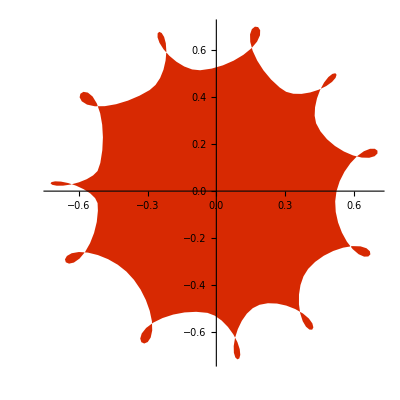

```mathematica
RandomPaintSplatter[ColorData["SolarColors"]]
```

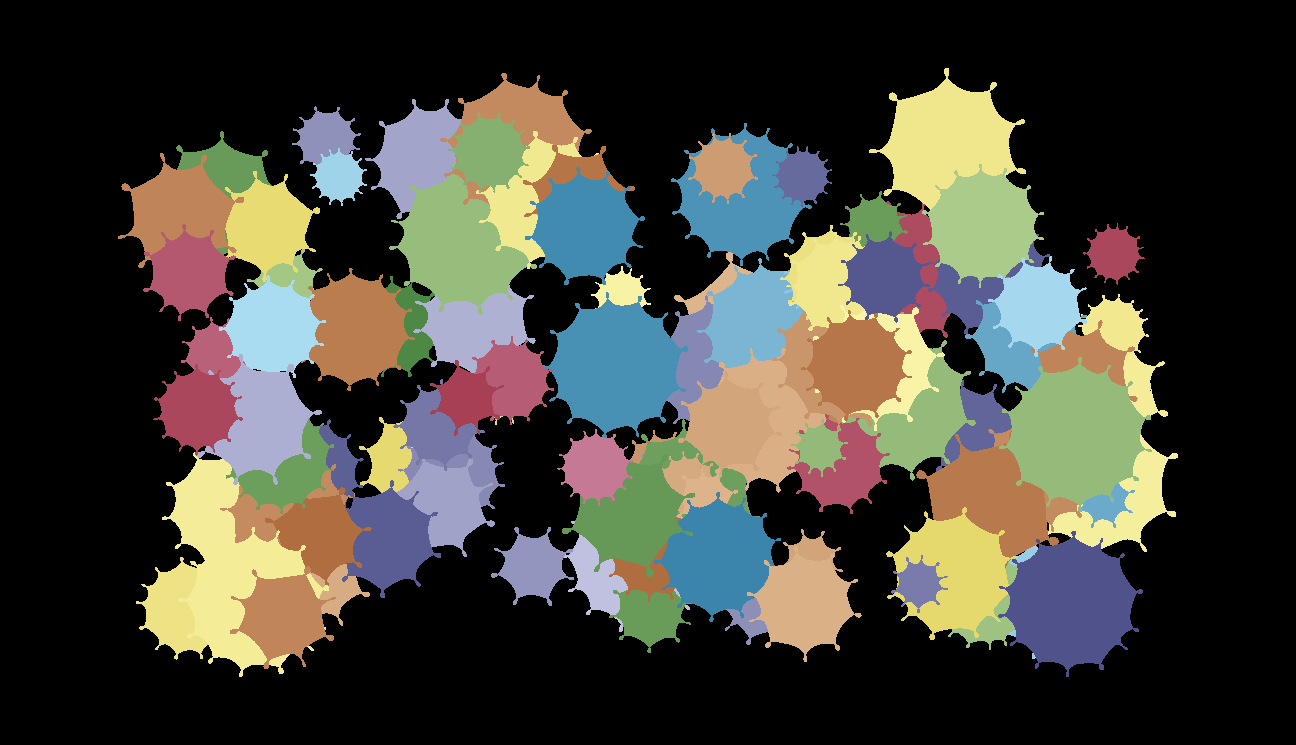

```mathematica
Show[
Table[
Graphics[
Translate[
RandomPaintSplatter[ColorData["DarkBands"]][[1]], {Random[Real,{-10,10}], Random[Real,{-5,5}]}]],
{i,0,100}],
Background -> Black,
ImageSize -> 50*72/2.54]
```